(2744 √7)/(15 π (7+1/36 (-14+x)^2)^4)

1/2+(8 (-14+x) ((33+10/63 (-14+x)^2+(5 (-14+x)^4)/21168)/(48 (1+1/252 (-14+x)^2)^3)+(15 √7 ArcTan[(-14+x)/(6 √7)])/(8 (-14+x))))/(15 √7 π)

ConditionalExpression[Piecewise[{{14-6 √7 √(-1+1/InverseBetaRegularized[2 x,7/2,1/2]), 0<x<1/2}, {14, x==1/2}, {14+6 √7 √(-1+1/InverseBetaRegularized[2 (1-x),7/2,1/2]), 1/2<x<1}, {-∞, x≤0}, {∞, True}}],0≤x≤1]

14

0.5

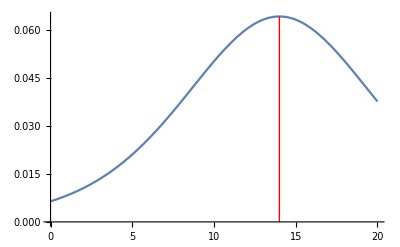

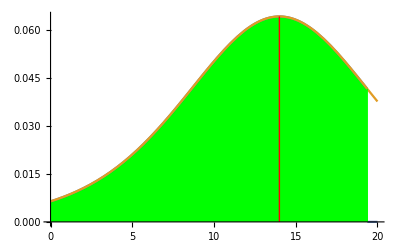

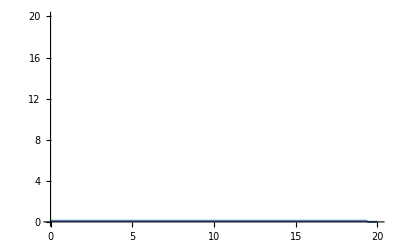

{-∞,22.4895}

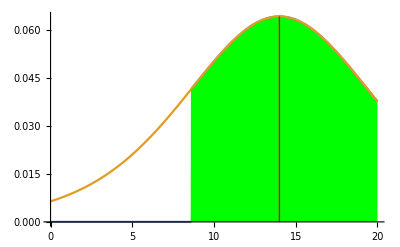

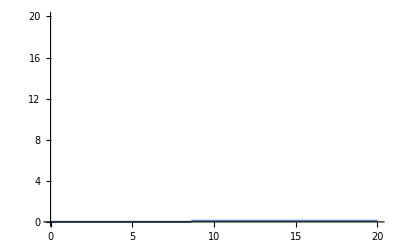

{5.51046,∞}

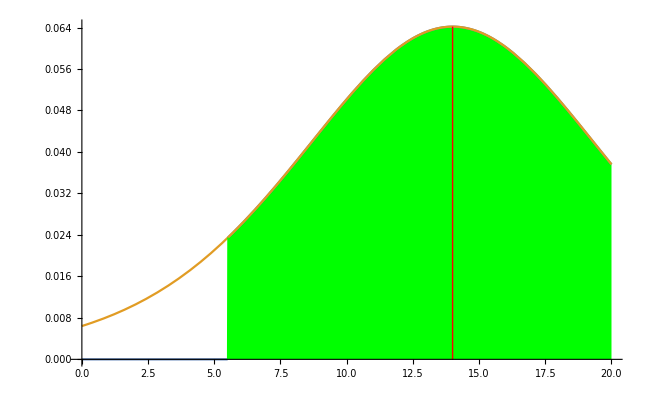
Symmertrisk:-Graphics-

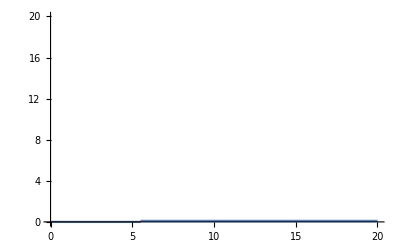

{2.63253,25.3675}

```mathematica
(*Data for plotting*)
(*Fyll inn og trykke <ctrl+enter>*)
μ:= 14;
σ := 6;
df := 7;

(*Endre her for å endre intervallet som tegnes på grafen*)
Nedre := 0;
Ovre := 20;

(*Konfidensintervallet*)
konfint := 0.90;


Temp:=StudentTDistribution[μ,σ,df];
f[t_]:=PDF[Temp,t];
F[t_]:=CDF[Temp,t];
Ff[t_]:=InverseCDF[Temp,t];

theInterval[t_,start_,end_]:=UnitStep[t-Ff[start]] (1-UnitStep[t-Ff[1-end]])
cF[t_,start_,end_]:=f[t] theInterval[t,start,end];
ciPlot[start_,end_,range_]:=Plot[{cF[x,start,end],f[x]},{x,Nedre,Ovre},PlotRange->All,Filling->{1->{Axis,{Green}},2->{{1},{White}}}]
ciIPlot[start_,end_,range_]:=Plot[0.1 theInterval[x,start,end],{x,Nedre,Ovre},PlotRange->{Nedre,Ovre},Filling->{1->{Axis,{Red}}}]
cendPlot[start_,end_,range_]:=Plot[{cF[x,start,end],f[x]},{x,0,1},PlotRange->All,Filling->{1->{Axis,{White}},2->{{1},{Red}}}]
f[x]
F[x]
Ff[x]
Mean[Temp]
F[Mean[Temp]]//N
Show[Plot[f[t],{t,Nedre,Ovre}],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]]

(*Venstre intervall*)

Show[
ciPlot[0,0.2,0.03],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]
]
ciIPlot[0,0.2,0.03]
{Ff[0.0],Ff[konfint]}

(*Høyre intervall*)
Show[
ciPlot[0.2,0,0.03],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]
]
ciIPlot[0.2,0,0.03]
{Ff[1-konfint],Ff[1]}

(*Symetriskkonfidensintervall om μ*)
Show[
ciPlot[F[Mean[Temp]]-0.4,0.6-F[Mean[Temp]],0.03],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]
]
ciIPlot[F[Mean[Temp]]-0.4,0.6-F[Mean[Temp]],0.03]
{Ff[F[Mean[Temp]]-konfint/2],Ff[F[Mean[Temp]]+konfint/2]}
```